## Bose-Hubbard model simulation

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<"../mathematica/mps_base.m"
```

### Bose-Hubbard Hamiltonian

```mathematica
SparseIdentityMatrix[d_]:=SparseArray[{i_,i_}->1,{d,d}]
```

```mathematica
SiteCreateOp[M_]:=DiagonalMatrix[Sqrt[Range[1,M]],-1]
SiteAnnihilOp[M_]:=DiagonalMatrix[Sqrt[Range[1,M]],1]
```

```mathematica
NumberOp[M_]:=DiagonalMatrix[Range[0,M]]
```

```mathematica
(* construct Bose-Hamiltonian with open boundary conditions *)
HBose[t_,U_,μ_,M_,1]:=U/2 NumberOp[M].(NumberOp[M]-IdentityMatrix[M+1])-μ NumberOp[M]
HBose[t_,U_,μ_,M_,L_]:=-t Sum[KroneckerProduct[SparseIdentityMatrix[(M+1)^(j-1)],SiteCreateOp[M],SiteAnnihilOp[M],SparseIdentityMatrix[(M+1)^(L-j-1)]]+KroneckerProduct[SparseIdentityMatrix[(M+1)^(j-1)],SiteAnnihilOp[M],SiteCreateOp[M],SparseIdentityMatrix[(M+1)^(L-j-1)]],{j,1,L-1}]+Sum[KroneckerProduct[SparseIdentityMatrix[(M+1)^(j-1)],U/2 NumberOp[M].(NumberOp[M]-IdentityMatrix[M+1])-μ NumberOp[M],SparseIdentityMatrix[(M+1)^(L-j)]],{j,1,L}]
```

### Simulation parameters

```mathematica
(* kinetic hopping parameter *)
Subscript[tH, val]=1;
```

```mathematica
(* interaction strength *)
Subscript[U, val]=5;
```

```mathematica
(* chemical potential *)
Subscript[μ, val]=1/7;
```

```mathematica
(* number of lattice sites *)
Subscript[L, val]=5;
```

```mathematica
(* single site occupation number cut-off *)
Subscript[M, val]=2;
```

```mathematica
Subscript[t, list]=Range[0,5,1/8];
Length[%]
```

41

### Out-of-time-order correlations

#### Read simulation results from disk

```mathematica
Subscript[fn, import]="../output/bose_hubbard/L"<>ToString[Subscript[L, val]]<>"_otoc_quench/bose_hubbard_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]];
```

```mathematica
Subscript[otoc1, list]=Import[Subscript[fn, import]<>"_otoc1.dat","Complex128"];
Dimensions[%]
```

{41}

```mathematica
(* example *)
Subscript[otoc1, list]⟦{1,2,-1}⟧
```

{1.+0. ⅈ,0.999258-0.0000871218 ⅈ,-0.227097-0.16506 ⅈ}

```mathematica
Subscript[otoc2, list]=Import[Subscript[fn, import]<>"_otoc2.dat","Complex128"];
Dimensions[%]
```

{41}

```mathematica
Subscript[gf, list]=Import[Subscript[fn, import]<>"_gf.dat","Complex128"];
Dimensions[%]
```

{41}

#### Reference calculation

```mathematica
GF[A_,B_,H_,ϕ_,t_]:=Module[{At=MatrixExp[-ⅈ t H].A.MatrixExp[ⅈ t H]},Tr[ϕ.At.B]/Tr[ϕ]]
```

```mathematica
OTOC[A_,B_,C_,D_,H_,ϕ_,t_]:=Module[{At=MatrixExp[-ⅈ t H].A.MatrixExp[ⅈ t H],Ct=MatrixExp[-ⅈ t H].C.MatrixExp[ⅈ t H]},Tr[ϕ.At.B.Ct.D]/Tr[ϕ]]
```

```mathematica
SiteCreateOpFull[j_,M_,L_]:=KroneckerProduct[SparseIdentityMatrix[(M+1)^j],SiteCreateOp[M],SparseIdentityMatrix[(M+1)^(L-j-1)]]
```

```mathematica
SiteAnnihilOpFull[j_,M_,L_]:=KroneckerProduct[SparseIdentityMatrix[(M+1)^j],SiteAnnihilOp[M],SparseIdentityMatrix[(M+1)^(L-j-1)]]
```

```mathematica
SiteNumberOpFull[j_,M_,L_]:=KroneckerProduct[SparseIdentityMatrix[(M+1)^j],NumberOp[M],SparseIdentityMatrix[(M+1)^(L-j-1)]]
```

```mathematica
Subscript[i, site]=1;
Subscript[j, site]=3;
```

```mathematica
(* MPO representing a factorized projector *)
Subscript[ϕ, state]=MPOMergeFull[Table[ArrayReshape[SparseArray[DiagonalMatrix[UnitVector[Subscript[M, val]+1,2]]],{Subscript[M, val]+1,Subscript[M, val]+1,1,1}],{j,Subscript[L, val]}]]
(* single non-zero entry *)
%//ArrayRules
```

SparseArray[<1>, {243, 243}]

{{122,122}→1,{_,_}→0}

```mathematica
Comm[A_,B_]:=A.B-B.A
```

```mathematica
(* ϕ does not commute with Hamiltonian *)
Comm[HBose[tH,U,μ,Subscript[M, val],Subscript[L, val]],Subscript[ϕ, state]]//ArrayRules
```

{{68,122}→-√2 tH,{104,122}→-√2 tH,{116,122}→-√2 tH,{120,122}→-√2 tH,{122,122}→0,{122,68}→√2 tH,{122,176}→√2 tH,{122,104}→√2 tH,{122,140}→√2 tH,{122,116}→√2 tH,{122,128}→√2 tH,{122,120}→√2 tH,{122,124}→√2 tH,{124,122}→-√2 tH,{128,122}→-√2 tH,{140,122}→-√2 tH,{176,122}→-√2 tH,{_,_}→0}

```mathematica
(* local density *)
Block[{tH=Subscript[tH, val],U=Subscript[U, val],μ=Subscript[μ, val],M=Subscript[M, val],L=Subscript[L, val],ϕ=Subscript[ϕ, state],HB},HB=N[HBose[tH,U,μ,M,L]];Table[Tr[ϕ.SiteNumberOpFull[i,M,L]],{i,0,L-1}]]
```

{1,1,1,1,1}

```mathematica
(* total energy *)
Block[{tH=Subscript[tH, val],U=Subscript[U, val],μ=Subscript[μ, val],M=Subscript[M, val],L=Subscript[L, val],ϕ=Subscript[ϕ, state],HB},HB=N[HBose[tH,U,μ,M,L]];Tr[ϕ.HB]]
(* only depends on μ *)
%+Subscript[L, val] Subscript[μ, val]
```

-0.714286

0.

```mathematica
Block[{tH=Subscript[tH, val],U=Subscript[U, val],μ=Subscript[μ, val],M=Subscript[M, val],L=Subscript[L, val],ϕ=Subscript[ϕ, state],HB},HB=N[HBose[tH,U,μ,M,L]];Subscript[otoc1, list,ref]=Table[OTOC[SiteCreateOpFull[Subscript[j, site],M,L],SiteCreateOpFull[Subscript[i, site],M,L],SiteAnnihilOpFull[Subscript[j, site],M,L],SiteAnnihilOpFull[Subscript[i, site],M,L],HB,ϕ,t],{t,Subscript[t, list]}]];
```

```mathematica
Block[{tH=Subscript[tH, val],U=Subscript[U, val],μ=Subscript[μ, val],M=Subscript[M, val],L=Subscript[L, val],ϕ=Subscript[ϕ, state],HB},HB=N[HBose[tH,U,μ,M,L]];Subscript[otoc2, list,ref]=Table[OTOC[SiteCreateOpFull[Subscript[j, site],M,L],SiteAnnihilOpFull[Subscript[i, site],M,L],SiteAnnihilOpFull[Subscript[j, site],M,L],SiteCreateOpFull[Subscript[i, site],M,L],HB,ϕ,t],{t,Subscript[t, list]}]];
```

```mathematica
Block[{tH=Subscript[tH, val],U=Subscript[U, val],μ=Subscript[μ, val],M=Subscript[M, val],L=Subscript[L, val],ϕ=Subscript[ϕ, state],HB},HB=N[HBose[tH,U,μ,M,L]];Subscript[gf, list,ref]=Table[GF[SiteCreateOpFull[Subscript[j, site],M,L],SiteAnnihilOpFull[Subscript[i, site],M,L],HB,ϕ,t],{t,Subscript[t, list]}]];
```

```mathematica
(* compare *)
Norm[Subscript[otoc1, list]-Subscript[otoc1, list,ref],∞]
```

0.0000533022

```mathematica
(* compare *)
Norm[Subscript[otoc2, list]-Subscript[otoc2, list,ref],∞]
```

0.000135836

```mathematica
(* compare *)
Norm[Subscript[gf, list]-Subscript[gf, list,ref],∞]
```

0.0000426509

#### Visualize results

```mathematica
Subscript[plot, label]="Bose-Hubbard model with\nt_H="<>ToString[Subscript[tH, val]]<>", U="<>ToString[Subscript[U, val]]<>", μ="<>ToString[InputForm[Subscript[μ, val]]]<>", M="<>ToString[Subscript[M, val]]<>", L="<>ToString[Subscript[L, val]]<>"\nsites: i="<>ToString[Subscript[i, site]]<>", j="<>ToString[Subscript[j, site]];
```

```mathematica
Subscript[fn, export]="plots/"<>#<>"/"<>#<>"_"&[FileBaseName[NotebookFileName[]]];
```

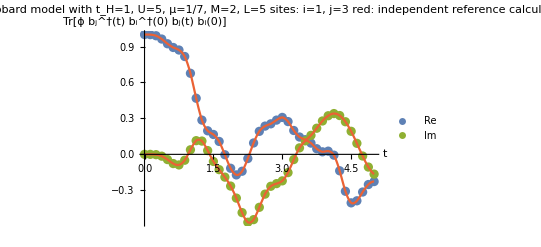

```mathematica
Show[ListPlot[{Transpose[{Subscript[t, list],Re[Subscript[otoc1, list]]}],Transpose[{Subscript[t, list],Im[Subscript[otoc1, list]]}]},AxesLabel->{"t","Tr[ϕ b_j^†(t) b_i^†(0) b_j(t) b_i(0)]"},PlotLabel->Subscript[plot, label]<>"\nred: independent reference calculation",PlotStyle->{ColorData[97][1],ColorData[97][3]},PlotLegends->{"Re","Im"}],Plot[{Interpolation[Transpose[{Subscript[t, list],Re[Subscript[otoc1, list,ref]]}]][τ],Interpolation[Transpose[{Subscript[t, list],Im[Subscript[otoc1, list,ref]]}]][τ]},{τ,0,5},PlotRange->All,PlotStyle->ColorData[97][4]]]
Export[Subscript[fn, export]<>"otoc1_L"<>ToString[Subscript[L, val]]<>".pdf",%];
```

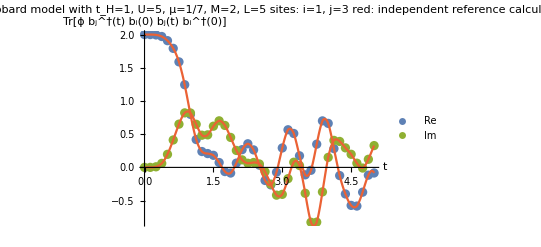

```mathematica
Show[ListPlot[{Transpose[{Subscript[t, list],Re[Subscript[otoc2, list]]}],Transpose[{Subscript[t, list],Im[Subscript[otoc2, list]]}]},AxesLabel->{"t","Tr[ϕ b_j^†(t) b_i(0) b_j(t) b_i^†(0)]"},PlotLabel->Subscript[plot, label]<>"\nred: independent reference calculation",PlotStyle->{ColorData[97][1],ColorData[97][3]},PlotLegends->{"Re","Im"}],Plot[{Interpolation[Transpose[{Subscript[t, list],Re[Subscript[otoc2, list,ref]]}]][τ],Interpolation[Transpose[{Subscript[t, list],Im[Subscript[otoc2, list,ref]]}]][τ]},{τ,0,5},PlotRange->All,PlotStyle->ColorData[97][4]]]
Export[Subscript[fn, export]<>"otoc2_L"<>ToString[Subscript[L, val]]<>".pdf",%];
```

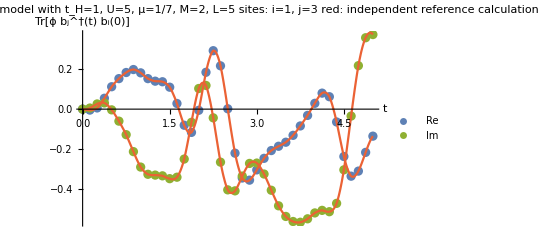

```mathematica
Show[ListPlot[{Transpose[{Subscript[t, list],Re[Subscript[gf, list]]}],Transpose[{Subscript[t, list],Im[Subscript[gf, list]]}]},AxesLabel->{"t","Tr[ϕ b_j^†(t) b_i(0)]"},PlotLabel->Subscript[plot, label]<>"\nred: independent reference calculation",PlotStyle->{ColorData[97][1],ColorData[97][3]},PlotLegends->{"Re","Im"}],Plot[{Interpolation[Transpose[{Subscript[t, list],Re[Subscript[gf, list,ref]]}]][τ],Interpolation[Transpose[{Subscript[t, list],Im[Subscript[gf, list,ref]]}]][τ]},{τ,0,5},PlotRange->All,PlotStyle->ColorData[97][4]]]
Export[Subscript[fn, export]<>"gf_L"<>ToString[Subscript[L, val]]<>".pdf",%];
```

### Virtual bond dimensions

```mathematica
Subscript[t, plot]={0,1/4,1/2,1,2,4};
```

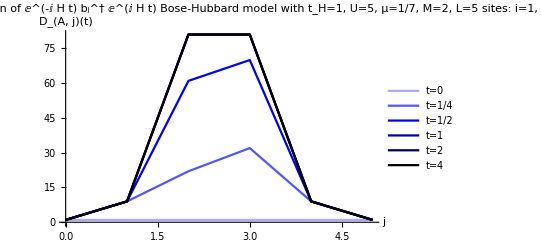

```mathematica
(* virtual bond dimension of ⅇ^(-ⅈ H t) Subscript[b, j]^† ⅇ^(ⅈ H t) operator *)
Partition[Import[Subscript[fn, import]<>"_D.dat","Integer64"],Subscript[L, val]+1];
%⟦#⟧&/@Flatten[Position[Subscript[t, list],#]&/@Subscript[t, plot]];
ListLinePlot[Transpose[{Range[0,Subscript[L, val]],#}]&/@%,AxesLabel->{"j","D_(A, j)(t)"},PlotRange->All,PlotLabel->"virtual bond dimension of ⅇ^(-ⅈ H t) b_j^† ⅇ^(ⅈ H t)\n"<>Subscript[plot, label],PlotStyle->{Lighter[Blue,2/3],Lighter[Blue,1/3],Blue,Darker[Blue,1/3],Darker[Blue,2/3],Black},PlotLegends->("t="<>ToString[InputForm[#]]&/@Subscript[t, plot])]
Export[Subscript[fn, export]<>"D_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]]<>".pdf",%];
```

### Effective truncation weight

```mathematica
(* tolerance (truncation weight) of ⅇ^(-ⅈ H t) Subscript[b, j]^† ⅇ^(ⅈ H t) operator *)
Norm[Partition[Import[Subscript[fn, import]<>"_tol_eff.dat","Real64"],Subscript[L, val]-1]-10^-10]
```

0.